## Initialization functions

Refractive indices and derivatives, walkoff and Snells law.

```mathematica
MatList={"BBO","YVO4","N-SF6HT","N-LAK22","KTP","Air"};
SellmAss = <|"BBO"-> {2.7359,0.01878,0.01822,0.01354,2.3753,0.01224,0.01667,0.01516},
		"YVO4"->{3.77834,0.069736,0.04724,0.0108133,4.59905,0.110534,0.04813,0.0122676} ,
"N-SF6HT"-> {1.77931763,0.0133714182,0.338149866,0.0617533621,2.08734474,174.01759},
"N-LAK22"-> {1.14229781,0.00585778594,0.535138441,0.0198546147,1.04088385,100.834017},
"KTP"-> {3.3134,0.05694,0.05658,0.01682,3.0333,0.04154,0.04547,0.01682},
"Air"-> {0,0}|>;

Sellmeier[a_,λ_]:=√(#[[1]]+(#[[2]])/((λ*1000)^2-#[[3]])-#[[4]]*(λ*1000)^2)&@a;

Sellmeierdλ[a_,λ_]:=D[Sellmeier[a,L],L]/.{L-> λ}
neeffect[θ_,ne_,no_]:=neeffect[θ,ne,no]=(1/(√(Sin[θ]^2/ne^2+Cos[θ]^2/no^2)));
nair[λ_]:=1.000287566+1.3412/((10^24*λ^2)/10^12);

nairdλ[lambda_]:=D[1.000287566+1.3412/((10^24*ll^2)/10^12),ll]/.{ll-> lambda};
CalcnForlens[λ_,a_]:=(1+(#[[1]]*λ^2)/(λ^2-#[[2]])+(#[[3]]*λ^2)/(λ^2-#[[4]])+(#[[5]]*λ^2)/(λ^2-#[[6]]))^(1/2)&@a;

nspecial[λ_]:=1.5;
nspecialdλ[λ_]:=0;

neeffectdλ[θ_,a_,λ_]:=-((-(Cos[θ]^2 (-(2000000 λ *a[[2]])/((1000000 λ^2-a[[3]])^2)-2000000 λ *a[[4]]))/((a[[1]]+a[[2]]/(1000000 λ^2-a[[3]])-1000000 λ^2 *a[[4]])^2)-((-(2000000 λ* a[[6]])/((1000000 λ^2-a[[7]])^2)-2000000 λ* a[[8]]) Sin[θ]^2)/((a[[5]]+a[[6]]/(1000000 λ^2-a[[7]])-1000000 λ^2 *a[[8]])^2))/(2 (Cos[θ]^2/(a[[1]]+a[[2]]/(1000000 λ^2-a[[3]])-1000000 λ^2 *a[[4]])+Sin[θ]^2/(a[[5]]+a[[6]]/(1000000 λ^2-a[[7]])-1000000 λ^2* a[[8]]))^(3/2)));

PropAngle[λ_,ω0_]:=λ/(π*ω0);
θdiv[ω0_,λ_]:=RandomVariate[NormalDistribution[0,PropAngle[λ,ω0]],{1,2}];
(*WalkOff[θ_,ne_,no_,length_]:=length*Tan[ArcTan[(ne/no)^2 θ]-θ];*)

WalkOff[θ_,a_,λ_,Length_]:=Length*1/2 neeffect[θ,Sellmeier[a[[5;;8]],λ],Sellmeier[a[[1;;4]],λ]]^2*((1/Sellmeier[a[[1;;4]],λ])^2-(1/Sellmeier[a[[5;;8]],λ])^2)*Sin[2θ];


Vgroup[Ray_,Object_]:=(2.998*10^11)/(Getn[Ray,Object]-Ray[λ]*Getndλ[Ray,Object]);

RefractAngle=Compile[{{nin,_Real},{nout,_Real},{ϕ,_Real}},ArcSin[nin/nout*Sin[ϕ]]];
RefractAngleCurve=Compile[{{pos,_Real},{nin,_Real},{nout,_Real},{ROC,_Real},{ϕ,_Real}},ArcSin[nin/nout*Sin[ϕ]]+pos*(nin-nout)/(nout*ROC)];
```

Crystal/ray defining, defining a setup

```mathematica
(*Defines a ray with the properties as mentioned, pos in mm, angles in rad, λ in mm, pol = ("H" or "V")*)
DefRay[Pos_,Vector_,lambda_,pol_]:=Association[position -> Pos,angles -> Vector,λ-> lambda,polarization-> pol];

(*Defines a crystal with the properties as mentioned, Orientation is defined as the direction that lies in the plane of ordinary polarization. Type = {"BBO","YVO4,"KTP"}, Pos = middle of crystal in MM. Lc = length in mm, orientation =( "left","up","right","down"),Cangle in rad*)
DefCrystal[Name_,Type_,Orientation_,pos_,Lc_,Cangle_]:=Association[name-> Name ,type-> Type,orientation -> Orientation,position -> pos, length -> Lc,cutangle -> Cangle];

(*Defines a lens. NAME HAS TO CONTAIN "lens" for this to work!! Type = (any material from material list), Orientation = NA, pos = middle in mm, lenght in mm, ROC is VECTOR {ROC front in mm, ROC back in mm}*)
DefLens[Name_,Type_,Orientation_,pos_,centre_,Lc_,RadiusofCurve_]:=Association[name-> Name ,type-> Type,orientation -> Orientation,position -> pos, length -> Lc,centrepos -> centre,ROC-> RadiusofCurve];

DefAchromat[pos_,centre_,thickness_,ROCu_,material_]:={Association[name-> "lens1" ,type-> material[[1]],orientation -> "none",position -> pos-(thickness[[1]]/2), length -> thickness[[1]],centrepos -> centre,ROC-> ROCu[[1]]],Association[name-> "lens2" ,type-> material[[2]],orientation -> "none",position -> pos+(thickness[[2]]/2), length -> thickness[[2]],centrepos -> centre,ROC-> ROCu[[2]]]};


(*Creates a list which can be displayed using Graphics to show the crystal*)
MakeCrystalVis[Crystal_]:={EdgeForm[Thick],Which[StringMatchQ[Crystal[type],"BBO"],Blue,StringMatchQ[Crystal[type],"YVO4"],GrayLevel[0.75],StringMatchQ[Crystal[type],"Air"],White,StringContainsQ[Crystal[name],"lens"],Purple],Rectangle[{Crystal[fsurf],-10},{Crystal[bsurf],10}]};

(*Creates the front and back surface of the crystal, as well as looking up the sellmeier coeff for he crystal type*)
CrystalSpecs[Crystal_]:=Module[{Type=Crystal[type]},Append[Crystal,{fsurf-> Crystal[position]-Crystal[length]/2,bsurf -> Crystal[position]+Crystal[length]/2,sellmcoeff -> SellmAss[Type]}]]

(*Automatically inserts Air in to setup between the crystals*)
GetAir[Setup_]:=Module[{Crystal1,Crystal2=Setup[[-1]],SetupWithAir=Setup},
For[i=Length[Setup],i≥ 2,i=i-1,Crystal1 = Setup[[i-1]]; Crystal2=Setup[[i]]; 
If[Crystal1[bsurf]≠ Crystal2[fsurf],SetupWithAir=Insert[SetupWithAir,DefCrystal["ConnectPieceAir","Air","None",Crystal1[bsurf]+(-Crystal1[bsurf]+ Crystal2[fsurf])/2,-Crystal1[bsurf]+ Crystal2[fsurf],"None"],i],"None"]];
If[Setup[[1]][fsurf]≠ 0,SetupWithAir=Prepend[SetupWithAir,DefCrystal["Start","Air","None",(Crystal1[fsurf])/2,Crystal1[fsurf],"None"]],"Nope"];
SetupWithAir=Append[SetupWithAir,DefCrystal["End","Air","None",Setup[[-1]][bsurf]+2,4,"None"]];
SetupWithAir](*Defines air surfaces in front,between and behind the crystal. If the first crystal doenst start at 0 air is added.*)

MakeSetupComplete[setup_]:=CrystalSpecs/@GetAir[CrystalSpecs /@ setup](*Function to go from a list of crystals without surfaces to a full setup with air and surfaces *)
 
(*Function that shows the path of the photon through the setup*)
ShowPath[Rays_,Setup_,dim_]:=Module[{Picture,coos},If[!AssociationQ[Rays],coos=TotalPropagation[#,Setup]&/@Rays;
Picture=Show[{Graphics[MakeCrystalVis/@Setup],ListLinePlot[#,PlotStyle-> Red]&/@coos[[All,dim,All]]}];
Return[Picture],coos=TotalPropagation[Rays,Setup];
Picture=Show[{Graphics[MakeCrystalVis/@Setup],ListLinePlot[coos[[dim,All]],PlotStyle-> Red]}]];
Return[Picture]]
```

## Making standard setups

```mathematica
ImprovedPostcompSetupSingle[Lpostc_]:=Module[{BBO1,BBO2,BBO3,BBO4,PostComp,SmallAirPiece,Setup},
BBO1=DefCrystal["BBO1","BBO","up",3,6,28.76*π/180];
BBO2=DefCrystal["BBO2","BBO","left",9,6,28.76*π/180]; 
BBO3=DefCrystal["BBO3","BBO","right",59,3,28.76*π/180];
BBO4=DefCrystal["BBO4","BBO","up",62,3,28.76*π/180];
PostComp= DefCrystal["PostComp","YVO4","down",72,Lpostc,π/2];
SmallAirPiece=DefCrystal["ExtraAir_Refract","Air","none",72+Lpostc/2,0.0000001];
Setup= {BBO1,BBO2,BBO3,BBO4,PostComp,SmallAirPiece};

Return[MakeSetupComplete[Setup]]]

RealAitorSetupSingle[Lpostc_]:=Module[{BBO1,BBO2,BBO3,BBO4,PostComp,SmallAirPiece,Setup},
BBO1=DefCrystal["BBO1","BBO","up",3,6,28.76*π/180];
BBO2=DefCrystal["BBO2","BBO","left",9,6,28.76*π/180]; 
BBO3=DefCrystal["BBO3","BBO","right",36,3,28.76*π/180];
BBO4=DefCrystal["BBO4","BBO","up",39,3,28.76*π/180];
PostComp= DefCrystal["PostComp","YVO4","down",114,Lpostc,π/2];
SmallAirPiece=DefCrystal["ExtraAir_Refract","Air","none",72+Lpostc/2,0.0000001];
Setup= {BBO1,BBO2,BBO3,BBO4,PostComp,SmallAirPiece};

Return[MakeSetupComplete[Setup]]]


ImprovedPostcompSetupSingleWithAC[Lpostc_,poslens_,posfocus_]:=Module[{BBO1,BBO2,BBO3,BBO4,PostComp,ACM,ExtraAir,Setup},
BBO1=DefCrystal["BBO1","BBO","up",3,6,28.7991*π/180];
BBO2=DefCrystal["BBO2","BBO","left",9,6,28.7991*π/180]; 
BBO3=DefCrystal["BBO3","BBO","right",59,3,28.7991*π/180];
BBO4=DefCrystal["BBO4","BBO","up",62,3,28.7991*π/180];
PostComp= DefCrystal["PostComp","YVO4","down",75,Lpostc,π/2];
ACM=DefAchromat[poslens,{-0.19,-0.19},{2.3,1.3},{{13.5,-10.6},{-10.6,-47.8}},{"N-SF6HT","N-LAK22"}];
ExtraAir=DefCrystal["ExtraAir","Air","none",poslens+1.3+posfocus/2,posfocus,"None"];

Setup= {BBO1,BBO2,BBO3,BBO4,PostComp,ACM[[1]],ACM[[2]],ExtraAir};

Return[MakeSetupComplete[Setup]]]
```

```mathematica
SetupBBO[]:=Module[{PreComp,BBO1,BBO2,BBO3,BBO4,PostComp,Setup},
PreComp=DefCrystal["PostComp","YVO4","down",-10,3.44,π/2];
BBO1=DefCrystal["BBO1","BBO","up",3,6,28.76*π/180];
BBO2=DefCrystal["BBO2","BBO","left",9,6,28.76*π/180]; 
BBO3=DefCrystal["BBO3","BBO","right",20,3,28.76*π/180];
BBO4=DefCrystal["BBO4","BBO","up",23,3,28.76*π/180];
PostComp= DefCrystal["PostComp","YVO4","down",40,3.12,π/2];
Setup= {PreComp,BBO1,BBO2,BBO3,BBO4,PostComp};

Return[MakeSetupComplete[Setup]]]

SetupKTP[]:=Module[{PreComp,KTP1,KTP2,PostComp,Setup},
PreComp=DefCrystal["PostComp","YVO4","down",-10,3.44,π/2];
KTP1=DefCrystal["BBO1","BBO","up",3,6,π/2];
KTP2=DefCrystal["BBO2","BBO","left",9,6,π/2]; 
PostComp= DefCrystal["PostComp","YVO4","down",20,3.12,π/2];
Setup= {PreComp,KTP1,KTP2,PostComp};

Return[MakeSetupComplete[Setup]]]
```

```mathematica
SetupBBOc[L_,tc_]:=Module[{BBO1,BBO2,BBO3,BBO4,PostComp,Setup},

BBO1=DefCrystal["BBO1","BBO","up",L[[2]]/2,L[[2]],tc];
BBO2=DefCrystal["BBO2","BBO","left",L[[2]]+L[[3]]/2,L[[3]],tc]; 
BBO3=DefCrystal["BBO3","BBO","right",30+L[[4]]/2,L[[4]],tc];
BBO4=DefCrystal["BBO4","BBO","up",30+L[[4]]+L[[5]]/2,L[[5]],tc];
PostComp= DefCrystal["PostComp","YVO4","up",60,L[[6]],π/2];
Setup= {BBO1,BBO2,BBO3,BBO4,PostComp};

Return[MakeSetupComplete[Setup]]]

SetupPumpcalc[L_,tc_]:=Module[{Air1,Air2,PreComp,BBO1,Setup1,Setup2},
Air1=DefCrystal["Air","Air","none",(10-L[[1]]/2)/2,10-L[[1]]/2,0];
PreComp=DefCrystal["PostComp","YVO4","up",10,L[[1]],π/2];
Air2=DefCrystal["Air","Air","none",10+L[[1]]/2+((30-L[[2]]/2)-(10+L[[1]]/2))/2,(30-L[[2]]/2)-(10+L[[1]]/2),0];
BBO1=DefCrystal["BBO1","BBO","up",30,L[[2]],tc];

Setup1= {Air1,PreComp,Air2};
Setup2= {Air1,PreComp,Air2,BBO1};

Return[{MakeSetupComplete[Setup1],MakeSetupComplete[Setup2]}]]
```

Ray Propagation

```mathematica
(*Function that gets the refractive index*)
Getn[Ray_,Object_]:=Which[StringMatchQ[Object[type],"Air"],nair[Ray[λ]],
						StringMatchQ[Object[type],"BBO"],CalcBiren[Ray,Object],
						StringMatchQ[Object[type],"YVO4"],CalcBiren[Ray,Object],
						StringMatchQ[Object[type],"KTP"],CalcBiren[Ray,Object],
						StringContainsQ[Object[name],"lens"],GetnLens[Ray,Object],
						StringMatchQ[Object[type],"Special"],nspecial[λ]
					]
(*Function that gets the refractive index derivative with respect to wavelenght*)
Getndλ[Ray_,Object_]:=Which[StringMatchQ[Object[type],"Air"],nairdλ[Ray[λ]],
						StringMatchQ[Object[type],"BBO"],CalcBirendλ[Ray,Object],
						StringMatchQ[Object[type],"YVO4"],CalcBirendλ[Ray,Object],
						StringMatchQ[Object[type],"KTP"],CalcBirendλ[Ray,Object],
						StringMatchQ[Object[type],"Special"],nspecialdλ[λ]
					]
GetnLens[Ray_,Object_]:=CalcnForlens[Ray[λ]*1000,Object[sellmcoeff]];

(*Function that calculates the refractive index in a birefringent crystal for a ray with incoming angles and certain polarization*)
CalcBiren[Ray_,Crystal_]:=Which[
	StringMatchQ[Crystal[orientation],"up"],Which[
			StringMatchQ[Ray[polarization],"V"],
				Sellmeier[Crystal[sellmcoeff][[1;;4]],Ray[λ]],
			StringMatchQ[Ray[polarization],"H"],
				neeffect[Crystal[cutangle]-Ray[angles][[2]],Sellmeier[Crystal[sellmcoeff][[5;;8]],Ray[λ]],Sellmeier[Crystal[sellmcoeff][[1;;4]],Ray[λ]]]],
	StringMatchQ[Crystal[orientation],"left"],Which[
			StringMatchQ[Ray[polarization],"V"],neeffect[Crystal[cutangle]-Ray[angles][[1]],Sellmeier[Crystal[sellmcoeff][[5;;8]],Ray[λ]],Sellmeier[Crystal[sellmcoeff][[1;;4]],Ray[λ]]],
			StringMatchQ[Ray[polarization],"H"],
				Sellmeier[Crystal[sellmcoeff][[1;;4]],Ray[λ]]],
	StringMatchQ[Crystal[orientation],"right"],Which[
			StringMatchQ[Ray[polarization],"V"],
				neeffect[-1*(Crystal[cutangle]+Ray[angles][[1]]),Sellmeier[Crystal[sellmcoeff][[5;;8]],Ray[λ]],Sellmeier[Crystal[sellmcoeff][[1;;4]],Ray[λ]]],
			StringMatchQ[Ray[polarization],"H"],
				Sellmeier[Crystal[sellmcoeff][[1;;4]],Ray[λ]]],
	StringMatchQ[Crystal[orientation],"down"],Which[
			StringMatchQ[Ray[polarization],"V"],
				Sellmeier[Crystal[sellmcoeff][[1;;4]],Ray[λ]],
			StringMatchQ[Ray[polarization],"H"],
				neeffect[-1*(Crystal[cutangle]+Ray[angles][[2]]),Sellmeier[Crystal[sellmcoeff][[5;;8]],Ray[λ]],Sellmeier[Crystal[sellmcoeff][[1;;4]],Ray[λ]]]]]

(*Function that calculates the refractive index derivative with respect to wavelength in a birefringent crystal for a ray with incoming angles and certain polarization*)
CalcBirendλ[Ray_,Crystal_]:=Which[
	StringMatchQ[Crystal[orientation],"up"],Which[
			StringMatchQ[Ray[polarization],"V"],
				Sellmeierdλ[Crystal[sellmcoeff][[1;;4]],Ray[λ]],
			StringMatchQ[Ray[polarization],"H"],
				neeffectdλ[Crystal[cutangle]-Ray[angles][[2]],Crystal[sellmcoeff],Ray[λ]]],
	StringMatchQ[Crystal[orientation],"left"],Which[
			StringMatchQ[Ray[polarization],"V"],neeffectdλ[Crystal[cutangle]-Ray[angles][[1]],Crystal[sellmcoeff],Ray[λ]],
			StringMatchQ[Ray[polarization],"H"],
				Sellmeierdλ[Crystal[sellmcoeff][[1;;4]],Ray[λ]]],
	StringMatchQ[Crystal[orientation],"right"],Which[
			StringMatchQ[Ray[polarization],"V"],
				neeffectdλ[-1*(Crystal[cutangle]+Ray[angles][[1]]),Crystal[sellmcoeff],Ray[λ]],
			StringMatchQ[Ray[polarization],"H"],
				Sellmeierdλ[Crystal[sellmcoeff][[1;;4]],Ray[λ]]],
	StringMatchQ[Crystal[orientation],"down"],Which[
			StringMatchQ[Ray[polarization],"V"],
				Sellmeierdλ[Crystal[sellmcoeff][[1;;4]],Ray[λ]],
			StringMatchQ[Ray[polarization],"H"],
				neeffectdλ[-1*(Crystal[cutangle]+Ray[angles][[2]]),Crystal[sellmcoeff],Ray[λ]]]]

(*Function that determines the walkoff in a Birefringent crystal*)
DetWalkoff[Ray_,Crystal_]:=Which[Ray[polarization]=="V",Which[Crystal[orientation]=="left",																									Re[WalkOff[Crystal[cutangle]-Ray[angles][[1]],Crystal[sellmcoeff],Ray[λ],Crystal[length]-(Ray[position][[3]]-Crystal[fsurf])]],
Crystal[orientation]=="right",Re[WalkOff[-1*(Crystal[cutangle]-Ray[angles][[1]]),Crystal[sellmcoeff],Ray[λ],Crystal[length]-(Ray[position][[3]]-Crystal[fsurf])]],
Crystal[orientation]=="up",0,
Crystal[orientation]=="down",0],
	Ray[polarization]=="H",
	Which[Crystal[orientation]=="up",Re[WalkOff[Crystal[cutangle]-Ray[angles][[2]],Crystal[sellmcoeff],Ray[λ],Crystal[length]-(Ray[position][[3]]-Crystal[fsurf])]],
			Crystal[orientation]=="down",Re[WalkOff[-1*(Crystal[cutangle]-Ray[angles][[2]]),Crystal[sellmcoeff],Ray[λ],Crystal[length]-(Ray[position][[3]]-Crystal[fsurf])]],
			Crystal[orientation]=="left",0,
			Crystal[orientation]=="right",0]]
(*Function that determines if an incoming beam is Extraordinary polarized, will return true if it is the case*)						
ExtPol[Ray_,Object_]:=If[Object[type]=="Air"||StringContainsQ[Object[name],"lens"],False,Which[Ray[polarization]=="H",If[Object[orientation]=="left" ||Object[orientation]=="right",False,True],Ray[polarization]=="V",If[Object[orientation]=="up" ||Object[orientation]=="down",False,True]]];

(*Function that calculates the translation of a ray through an object (Air or Crystal), it will automatically decide if it has to include walkoff*)
Trans[Ray_,Object_]:=If[Ray[position][[3]]>Object[bsurf],Ray,
If[StringMatchQ[Object[type],"Air"]||StringMatchQ[Object[type],"Special"],
Block[{translation = TranslationTransform[Re[{(Object[length]-(Ray[position][[3]]-Object[fsurf]))*Tan[Ray[angles][[1]]],(Object[length]-(Ray[position][[3]]-Object[fsurf]))*Tan[Ray[angles][[2]]],(Object[length]-(Ray[position][[3]]-Object[fsurf]))}]]},Append[Ray,position-> translation[Ray[position]]]],
				If[!ExtPol[Ray,Object],Block[{translation = TranslationTransform[Re[{(Object[length]-(Ray[position][[3]]-Object[fsurf]))*Tan[Ray[angles][[1]]],(Object[length]-(Ray[position][[3]]-Object[fsurf]))*Tan[Ray[angles][[2]]],(Object[length]-(Ray[position][[3]]-Object[fsurf]))}]]},Append[Ray,position-> translation[Ray[position]]]],Block[{translation = {}}, If[Ray[polarization]=="V",translation =TranslationTransform[Re[{DetWalkoff[Ray,Object],(Object[length]-(Ray[position][[3]]-Object[fsurf]))*Tan[Ray[angles][[2]]],(Object[length]-(Ray[position][[3]]-Object[fsurf]))}]],translation = TranslationTransform[Re[{(Object[length]-(Ray[position][[3]]-Object[fsurf]))*Tan[Ray[angles][[1]]],DetWalkoff[Ray,Object],(Object[length]-(Ray[position][[3]]-Object[fsurf]))}]]];Append[Ray,position-> translation[Ray[position]]]]]]]

(*Function that calculates the refraction at an interface between two objects*)
RayRefract[Ray_,Obj1_,Obj2_]:=
If[!(ExtPol[Ray,Obj2]),
If[!(StringContainsQ[Obj1[name],"lens"]||StringContainsQ[Obj2[name],"lens"]),Block[{nin=Getn[Ray,Obj1],nout=Getn[Ray,Obj2],αin = Ray[angles],αout},αout={RefractAngle[nin,nout,αin[[1]]],RefractAngle[nin,nout,αin[[2]]]};Append[Ray,angles-> αout]],
Which[StringContainsQ[Obj1[name],"lens"]&&!StringContainsQ[Obj2[name],"lens"],Block[{nin=Getn[Ray,Obj1],nout=Getn[Ray,Obj2],αin = Ray[angles],ROC = Obj1[ROC][[2]],posonlens=Ray[position][[{1,2}]]-Obj1[centrepos],αout},αout={RefractAngleCurve[posonlens[[1]],nin,nout,ROC,αin[[1]]],RefractAngleCurve[posonlens[[2]],nin,nout,ROC,αin[[2]]]};Append[Ray,angles-> αout]],
!StringContainsQ[Obj1[name],"lens"]&&StringContainsQ[Obj2[name],"lens"],
Block[{nin=Getn[Ray,Obj1],nout=Getn[Ray,Obj2],αin = Ray[angles],ROC = Obj2[ROC][[1]],posonlens=Ray[position][[{1,2}]]-Obj2[centrepos],αout},αout={RefractAngleCurve[posonlens[[1]],nin,nout,ROC,αin[[1]]],RefractAngleCurve[posonlens[[2]],nin,nout,ROC,αin[[2]]]};Append[Ray,angles-> αout]],
StringContainsQ[Obj1[name],"lens"]&&StringContainsQ[Obj2[name],"lens"],Block[{nin=Getn[Ray,Obj1],nout=Getn[Ray,Obj2],αin = Ray[angles],ROC = Obj1[ROC][[2]],posonlens=Ray[position][[{1,2}]]-Obj2[centrepos],αout},αout={RefractAngleCurve[posonlens[[1]],nin,nout,ROC,αin[[1]]],RefractAngleCurve[posonlens[[2]],nin,nout,ROC,αin[[2]]]};Append[Ray,angles-> αout]]]],
If[Ray[polarization] =="H",Block[{nin=Getn[Ray,Obj1],nout=Getn[Ray,Obj2],αin = Ray[angles],αout},αout={RefractAngle[nin,nout,αin[[1]]],αin[[2]]};Append[Ray,angles-> αout]],
Block[{nin=Getn[Ray,Obj1],nout=Getn[Ray,Obj2],αin = Ray[angles],αout},αout={αin[[1]],RefractAngle[nin,nout,αin[[2]]]};
Append[Ray,angles-> αout]]]]

(*Function that propagates from fsurf of object 1 to fsurf of object 2. It consists of a translation followed by a refraction*)
Propagate[Ray_,Obj1_,Obj2_]:=RayRefract[Trans[Ray,Obj1],Obj1,Obj2];

(*This function handles all the propagation through the setup, and returns the {x,z}, {y,z} and the {x,y,z} coordinates at each interface*)
TotalPropagation[Ray_,Setup_]:=Block[{testray=Ray,groupedsetup=Partition[Setup,2,1],positions={Ray[position]}},For[i=1,i≤ Length[groupedsetup],i++,testray = Propagate[testray,groupedsetup[[i,1]],groupedsetup[[i,2]]];positions=Append[positions,testray[position]];];
{positions[[All,{3,1}]],positions[[All,{3,2}]],positions,testray[angles]}]

(*TotalPropagation[Ray_,Setup_]:=Block[{testray=Ray,groupedsetup=Group[Setup],positions={Ray[position]}},For[i=1,i≤ Length[groupedsetup],i++,testray = Propagate[testray,groupedsetup[[i,1]],groupedsetup[[i,2]]];positions=Append[positions,testray[position]];];{positions[[All,{3,1}]],positions[[All,{3,2}]],positions,testray[angles]}]*)

(*This function handles all the propagation through the setup, and returns the {α,β} angles at each interface*)

TotalPropagationAngles[Ray_,Setup_]:=Block[{testray=Ray,groupedsetup=Partition[Setup,2,1],Angles={Ray[angles]}},For[i=1,i≤ Length[groupedsetup],i++,testray = Propagate[testray,groupedsetup[[i,1]],groupedsetup[[i,2]]];Angles=Append[Angles,testray[angles]];];Return[Angles]]

TotalPropagationRay[Ray_,Setup_]:=Block[{testray=Ray,groupedsetup=Partition[Setup,2,1],positions={Ray[position]}},For[i=1,i≤ Length[groupedsetup],i++,testray = Propagate[testray,groupedsetup[[i,1]],groupedsetup[[i,2]]];AppendTo[positions,testray[position]];];
Return[{testray,positions}]]

(*Defines a random origin for the spdc photon to be emitted, depending on the walkoff of the pump in the BBO crystal*)
GetRandomOrigin[pumpRay_,Crystal_]:=Block[{rand=RandomVariate[UniformDistribution[]]},
		Which[StringMatchQ[pumpRay[polarization],"V"],
				Return[{rand*DetWalkoff[pumpRay,Crystal],0,rand*Crystal[length]}],
			StringMatchQ[pumpRay[polarization],"H"],
				Return[{0,rand*DetWalkoff[pumpRay,Crystal],rand*Crystal[length]}]]];
```

Direct phase difference functions

```mathematica
(*Function that propagates ray1(ray2) trought setup1(setup2), and multiplies the distance travled with the phase velocity of the ray, calculating the difference in phase*)
PhaseDiff[ray1_,ray2_,Setup1_,Setup2_]:= (Norm/@Differences[TotalPropagation[ray1,Setup1][[3]]]).((2π*(Getn[ray1,#]&/@Setup1[[1;;-2]]))/ray1[λ])-(Norm/@Differences[TotalPropagation[ray2,Setup2][[3]]]).((2π(Getn[ray2,#]&/@Setup2[[1;;-2]]))/ray2[λ])

(*Function that propagates ray1(ray2) trought setup1(setup2), and gives the difference in optical path*)
OptPathDiff[ray1_,ray2_,Setup1_,Setup2_]:=(Norm/@Differences[TotalPropagation[ray1,Setup1][[3]]]).(Getn[ray1,#]&/@Setup1[[1;;-2]])-(Norm/@Differences[TotalPropagation[ray2,Setup2][[3]]]).(Getn[ray2,#]&/@Setup2[[1;;-2]])

(*Function that propagates ray1(ray2) trought setup1(setup2), and gives the sum of optical path*)
OptPathSum[ray1_,ray2_,Setup1_,Setup2_]:=(Norm/@Differences[TotalPropagation[ray1,Setup1][[3]]]).(Getn[ray1,#]&/@Setup1[[1;;-2]])+(Norm/@Differences[TotalPropagation[ray2,Setup2][[3]]]).(Getn[ray2,#]&/@Setup2[[1;;-2]])

(*Function that propagates ray1 trought setup1 and gives the total optical path traveled*)
ArrivalTime[ray1_,Setup1_]:=(Norm/@Differences[TotalPropagation[ray1,Setup1][[3]]]).(Getn[ray1,#]&/@Setup1[[1;;-2]]);

(*Same as ArrivalTime, but uses group velocity*)
ArrivalTimeGV[ray1_,Setup1_]:=(Norm/@Differences[TotalPropagation[ray1,Setup1][[3]]]).(Vgroup[ray1,#]&/@Setup1[[1;;-2]])^-1;

(*Calculates τ_+ and τ_- for a given list of Arrival times in the order {SigH,IdlH,SigV,IdlV}*)
Calctptm[ArTimes_]:={ArTimes[[1]]-ArTimes[[2]],ArTimes[[3]]-ArTimes[[4]],(ArTimes[[1]]+ArTimes[[2]])/2,(ArTimes[[3]]+ArTimes[[4]])/2};
ArrivalTimePointAngle[ray1_,Setup1_]:=Module[{CompleteProp=TotalPropagation[ray1,Setup1]},Return[{(Norm/@Differences[CompleteProp[[3]]]).(Getn[ray1,#]&/@Setup1[[1;;-2]]),CompleteProp[[3,-1]],CompleteProp[[4]]}]]


ArrivalTimeVec[ray1_,Setup1_]:=Block[{CompleteProp=TotalPropagationRay[ray1,Setup1]},Return[{CompleteProp[[1]],(Norm/@Differences[CompleteProp[[2]]]).(Getn[ray1,#]&/@Setup1[[1;;-2]])}]]
```

## Fidelity from time difference (see R. Rangarajan Opt. Express, 17(21):18920{18933}) For this chapter, length in υm, angle in degree

```mathematica
(*We use the approach mentioned in this paper to calcucalte the Joint Two Photon Amplitude for the SPDC process*)
```

```mathematica
(*Module that computes the Sinc^2(Δk*L/2) for a given set of inputs, and doest this relatively quickly*)

phasefunctionIIcomp[thetas_,λs_,λi_,Lcryst_,cangle_]:=Module[
{Φ,λp=0.405,pump=0.5,nop,nep,nos,nes,noi,nei,nairs,nairi},
nop=ordindexcomp[λp];
nep=extindexcomp[λp];
nos=ordindexcomp[λs];
nes=extindexcomp[λs];
noi=ordindexcomp[λi];
nei=extindexcomp[λi];
nairi=airindexcomp[λi];
nairs=airindexcomp[λs];

Φ=phasecorecomp[pump,Lcryst,cangle,thetas,λp,λs,λi,nop,nep,nos,nes,noi,nei,nairs,nairi];
Return[Φ];
];
```

```mathematica
ordindexcomp=Compile[{{λ,_Real}},√(2.7359+0.01878/(λ λ-0.01822)-0.01354 λ λ),RuntimeAttributes->{Listable}];
extindexcomp=Compile[{{λ,_Real}},√(2.3753+0.01224/(λ λ-0.01667)-0.01516 λ λ),RuntimeAttributes->{Listable}];
airindexcomp=Compile[{{λ,_Real}},1.000287566+1.3412/((10^18 (λ λ))/10^12),RuntimeAttributes->{Listable}];
```

```mathematica
(*Complied function of the phasematching Sinc^2 for quick evaluations*)
```

```mathematica
phasecorecomp=Compile[{{pump,_Real},{Lcryst,_Real},{cangle,_Real},{thetas,_Real},{λp,_Real},{λs,_Real},{λi,_Real},{nop,_Real},{nep,_Real},{nos,_Real},{nes,_Real},{noi,_Real},{nei,_Real},{nairs,_Real},{nairi,_Real}},Exp[-(pump^2)*( (-nos*(2*π/λs)*Sin[ArcSin[Sin[thetas*π/180]*nairs/nos]] + noi*(2*π/λi)*Sin[ArcSin[nos*(2*π/λs)*Sin[ArcSin[Sin[thetas*π/180]*nairs/nos]]/(noi*(2*π/λi))]])^2)/2]*(Sin[(Sqrt[1/((Cos[cangle*π/180]/nop)^2 + (Sin[cangle*π/180]/nep)^2)]*(2*π/λp) -nos*(2*π/λs)*Cos[ArcSin[Sin[thetas*π/180]*nairs/nos]] - noi*(2*π/λi)*Cos[ArcSin[nos*(2*π/λs)*Sin[ArcSin[Sin[thetas*π/180]*nairs/nos]]/(noi*(2*π/λi))]])*Lcryst/2]/((Sqrt[1/((Cos[cangle*π/180]/nop)^2 + (Sin[cangle*π/180]/nep)^2)]*(2*π/λp) -nos*(2*π/λs)*Cos[ArcSin[Sin[thetas*π/180]*nairs/nos]] - noi*(2*π/λi)*Cos[ArcSin[nos*(2*π/λs)*Sin[ArcSin[Sin[thetas*π/180]*nairs/nos]]/(noi*(2*π/λi))]])*Lcryst/2))^2,RuntimeOptions->"Speed",RuntimeAttributes-> {Listable},Parallelization->True];
```

```mathematica
(*Plot of this phasefuntion NOTE!!! λ and L are  in υm, Subscript[θ, c] and θs are in degree, *)
ListDensityPlot[Table[phasefunctionIIcomp[theta,signal,(signal*0.405)/(signal - 0.405),6000,28.7996],{theta,-3,3,0.01},{signal,0.750,0.880,0.001}],PlotLegends->Automatic,PlotRange -> {0,1},DataRange-> {{0.750,0.880},{-3,3}}]
```

-Graphics-

```mathematica
(*Use this to calculate the JTPA NOTE THIS FUNCTION NEEDS TO BE NORMALIZED IF YOU CHANGE THE PARAMETERS/INTEGRATION AREA ts,ti in s,
σp λp in nm *)
```

```mathematica
JTPASL[ts_,ti_,σp_,λp_]:=Exp[-I*(2π*3*10^8)/λp*(ts+ti)/2]/(2π)*1/(√0.0033888749417149353)Total[Table[Exp[-I*(vs*ts+ti*vi)]*Exp[-((vs+vi)/((2π*3*10^8)/σp))^2]*phasefunctionIIcomp[0,(vs/(3*10^8*2π)+0.5/λp)^-1*10^6,(vi/(3*10^8*2π)+0.5/λp)^-1*10^6,6000,28.7991],{vs,0,(3*10^8*2π)/(775*10^-9)-(3*10^8*π)/(405*10^-9),0.05*10^14},{vi,(3*10^8*2π)/(845*10^-9)-(3*10^8*π)/(405*10^-9),0,0.05*10^14}],2]
```

```mathematica
(*Plot of the normalized two photon amplitude*)
```

```mathematica
NJTPA=Table[Norm[JTPASL[a*10^-15,b*10^-15,10^-9,405*10^-9]^2],{a,-200,200,10},{b,-200,200,10}];
```

```mathematica
NormConstantSqrd=Total[NJTPA,2]
```

1.

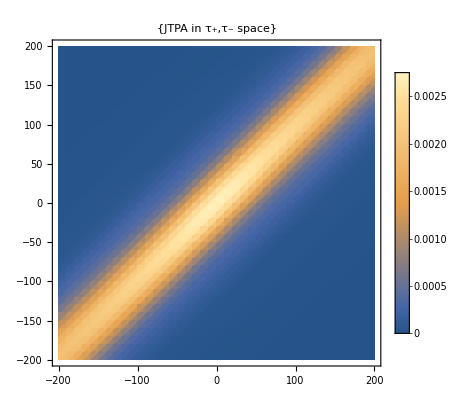

```mathematica
ListDensityPlot[NJTPA,PlotRange-> {0,1},PlotLegends-> Automatic,PlotLabel->{"JTPA in τ_+,τ_- space"},DataRange->{{-200,200},{-200,200}}]
```

```mathematica
(*We are now ready to calculate the coherence for a given delay*)
```

```mathematica
Coherence[t1_,t2_]:=Total[Table[JTPASL[a*10^-15+t1,b*10^-15+t2,10^-9,405*10^-9]*Conjugate[JTPASL[a*10^-15,b*10^-15,10^-9,405*10^-9]],{a,-200,200,10},{b,-200,200,10}],2];
```

```mathematica
((405*10^-9)^2)/(3*10^8*10^-9)//N
```

5.4675×10^-13

```mathematica
Coherence[0,0]
```

1.21773+0. ⅈ

```mathematica
(*Use it to calculate the JTPA coherence when changing the τ_+ delay in magnitude in orders of the pump*)
```

```mathematica
CohList
```

{{-2.9,-0.998139+0.0609847 ⅈ},{-2.5,-0.189472-0.981886 ⅈ},{-2.1,0.211605-0.977356 ⅈ},{-1.7,0.881133-0.472873 ⅈ},{-1.3,-0.260855-0.965395 ⅈ},{-0.9,0.983816+0.179989 ⅈ},{-0.5,0.979169-0.211609 ⅈ},{-0.1,-0.796189+0.631371 ⅈ}}

```mathematica
CohList=Table[{n,Coherence[10^n*(5.4675*10^-13)/2,-10^n*(5.4675*10^-13)/2]},{n,-2.9,0.1,0.2}];
```

$Aborted

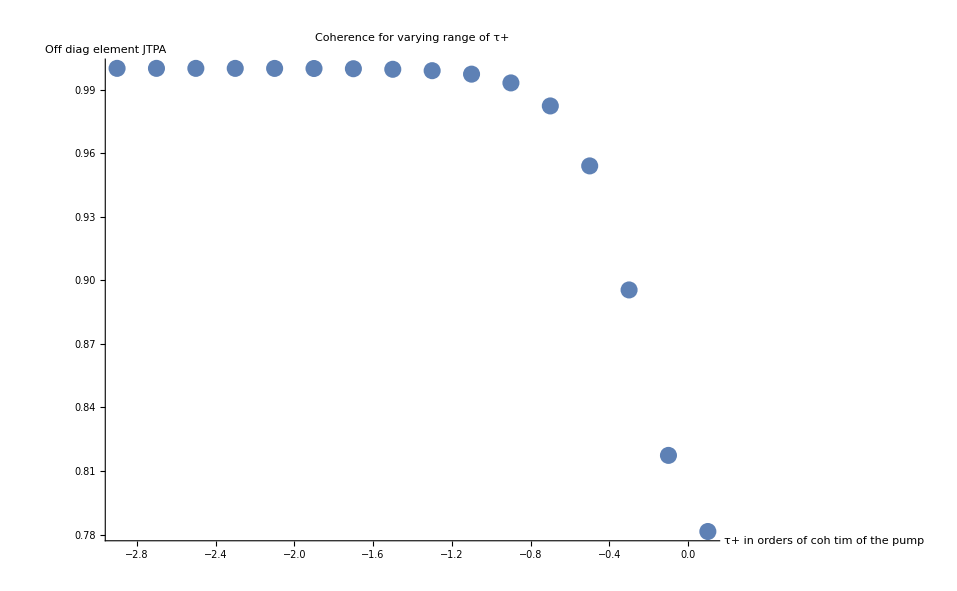

```mathematica
ListPlot[{CohList[[All,1]],Norm/@CohList[[All,2]]}ᵀ,PlotLabel->"Coherence for varying range of τ+",AxesLabel-> {"τ+ in orders of coh tim of the pump","Off diag element JTPA"}]
```

```mathematica
Coherence[10^3*5.4675*10^-13,10^3*5.4675*10^-13]//Norm
```

0.0108516

## Calculate time difference of H and V

```mathematica
(*This chapter explains how to calculate the arrival times of signal and idler pairs from the different crystals for a given opening angle*)
```

```mathematica
(*Constants for this simulation*)

θc=28.799 *π/180;
λp = 0.000405;
δλ = 1*10^-6;
λs = 0.000785;
λi=(λp*λs)/(λs-λp);
(*Use the functions defined earlier to simulate the propagation of all the rays in the setup (NOTE pump is simulated separately and added to the arrival times. L={a,b,c,d,e,f} is the vector with all the lenghts of the crystal )*)

TimeAnalysis[λp_,λs_,λi_,α_,β_,L_,tc_]:=Module[{setup,pumprays,SPDCrays,timespump,timesSPDC,TotalTime,tmin,tplus},
setup =SetupBBOc[L,tc];
pumprays={DefRay[{0,0,0},{0,0},λp,"H"],DefRay[{0,0,0},{0,0},λp,"V"]};
SPDCrays= {DefRay[{0,0,L[[2]]/2},{α,β},λs,"V"],DefRay[{0,0,L[[2]]/2},-{α,β},λi,"V"],DefRay[{0,0,L[[2]]+L[[3]]/2},{α,β},λs,"H"],DefRay[{0,0,L[[2]]+L[[3]]/2},-{α,β},λi,"H"]};
timespump = {ArrivalTimeGV[pumprays[[1]],SetupPumpcalc[L,tc][[1]]],ArrivalTimeGV[pumprays[[2]],SetupPumpcalc[L,tc][[2]]]};
timesSPDC= ArrivalTimeGV[#,setup]&/@SPDCrays ;
TotalTime=timesSPDC+Flatten[Outer[Times,{1,1},timespump]ᵀ];
tmin=TotalTime.{1,-1,-1,1};
tplus=1/2 TotalTime.{1,1,-1,-1};
Return[{tmin,tplus}]];
```

```mathematica
(*Show the compensation for different wavelenghts*)

Manipulate[ListLogPlot[{Table[{ii,((ii*10^-9)^2)/(3*10^8*Dλ*10^-9*π)*10^15},{ii,750,900,1}],Table[{x,Abs[TimeAnalysis[0.000405,x*10^-6,(0.000405*x*10^-6)/(x*10^-6-0.000405),α*π/180,β*π/180,{3.44,6,6,6/2,6/2,L},28.7996*π/180][[1]]*10^15]},{x,750,900,1}]},ImageSize-> Large,PlotRange->All,GridLines->{{{785-Dλ/2,Thick},{785+Dλ/2,Thick}},{{0,White},-.5,.5,{0,White}}},AxesLabel-> {"Signal wavelength [nm]","Coherence time [fs]"},DataRange-> {750,900}],{L,0,4,0.01},{α,-1,1,0.01},{β,-3,3,0.1},{Dλ,1,100,1}]
```

```mathematica
(*Now use this function to look at the dependence of the arrival times with angle *)
```

```mathematica
TimingData=Table[TimeAnalysis[λp,λs,λi,x*π/180,y*π/180,{3.41,6,6,3,3,3.14},θc]*10^15,{x,-1,1,0.05},{y,-1,1,0.05}];
```

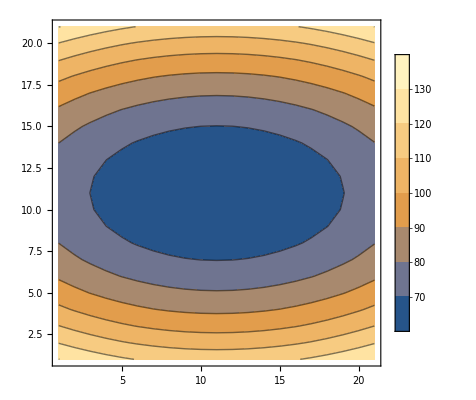

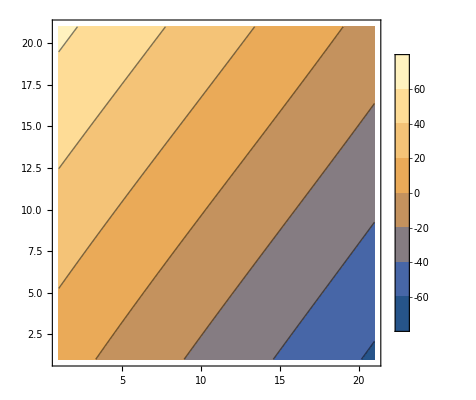

```mathematica
ListContourPlot[TimingData[[All,All,2]],PlotLegends-> Automatic]
ListContourPlot[TimingData[[All,All,1]],PlotLegends-> Automatic]
```

```mathematica
(*We can also look at the effect of crystal length deviations*)
```

```mathematica
ErrorDueToCryst=Table[10^15*TimeAnalysis[0.000405,0.000785,0.000832,0,0,#,28.7996*π/180]&/@((Map[RandomVariate[NormalDistribution[#[[1]],#[[2]]],{5000}]&,{{3.41,x},{6,x},{6,x},{3,x},{3,x},{3.14,x}}])ᵀ),{x,0.01,0.1,0.03}];
```

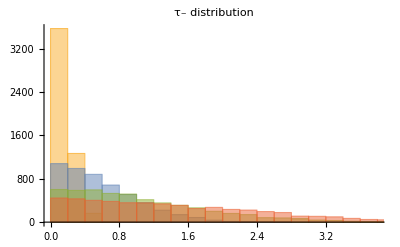

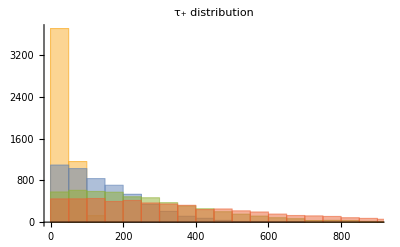

```mathematica
Histogram[Abs[ErrorDueToCryst[[All,All,1]]],PlotLabel-> "τ_- distribution"]
Histogram[Abs[ErrorDueToCryst[[All,All,2]]],PlotLabel-> "τ_+ distribution"]
```

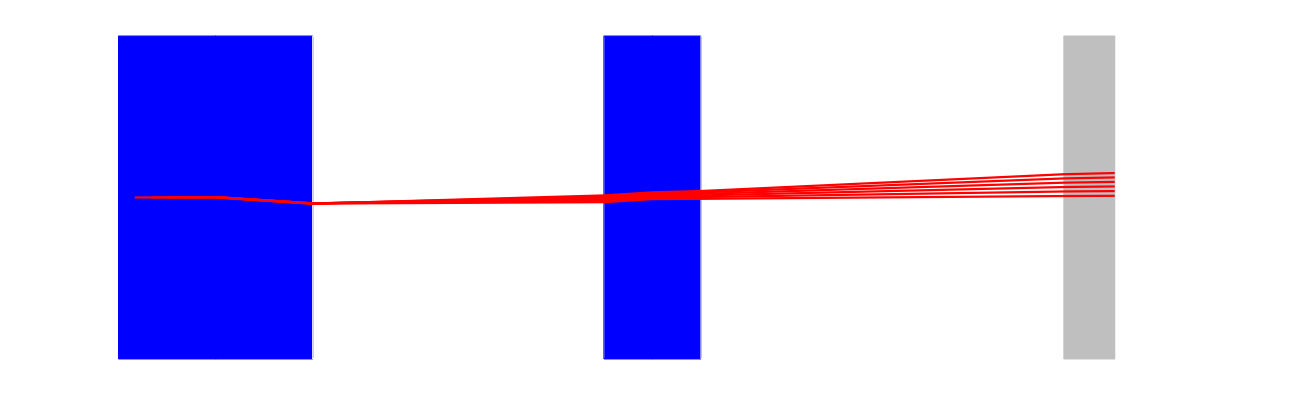

```mathematica
ShowPath[DefRay[{0,0,#},{#/6 π/180,-#/6 π/180},0.000785,"V"]&/@{1,2,3,4,5,6},SetupBBOc[{3.41,6,6,3,3,3.14},28.7996],1]
```

```mathematica
BBO1=DefCrystal["BBO1","BBO","up",3,6,π/180*28];
BBO2=DefCrystal["BBO1","BBO","left",9,6,π/180*28];
Setup=MakeSetupComplete[{BBO1,BBO2}];
```

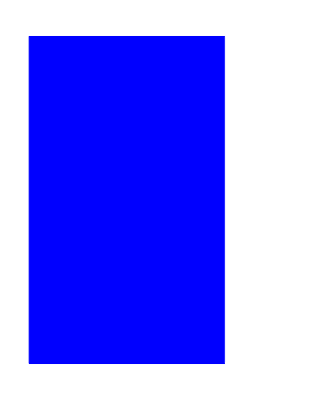

```mathematica
Show[Graphics[MakeCrystalVis/@Setup]]
```

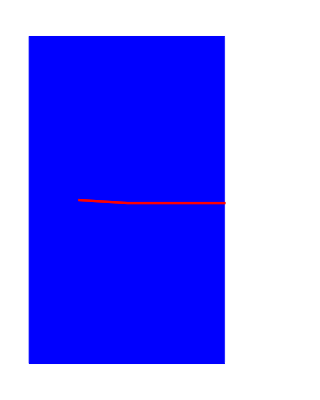

```mathematica
Ray1=DefRay[{0,0,3},{4*π/180,0},0.000785,"H"];
Ray2=DefRay[{0,0,3},{-4*π/180,0},0.000785,"H"];
ShowPath[{Ray1,Ray2},Setup,2]
```